```mathematica
KnotData["Hyperbolic"]
```

{{0,1},{4,1},{5,2},{6,1},{6,2},{6,3},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,20},{8,21},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{9,26},{9,27},{9,28},{9,29},{9,30},{9,31},{9,32},{9,33},{9,34},{9,35},{9,36},{9,37},{9,38},{9,39},{9,40},{9,41},{9,42},{9,43},{9,44},{9,45},{9,46},{9,47},{9,48},{9,49},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{10,26},{10,27},{10,28},{10,29},{10,30},{10,31},{10,32},{10,33},{10,34},{10,35},{10,36},{10,37},{10,38},{10,39},{10,40},{10,41},{10,42},{10,43},{10,44},{10,45},{10,46},{10,47},{10,48},{10,49},{10,50},{10,51},{10,52},{10,53},{10,54},{10,55},{10,56},{10,57},{10,58},{10,59},{10,60},{10,61},{10,62},{10,63},{10,64},{10,65},{10,66},{10,67},{10,68},{10,69},{10,70},{10,71},{10,72},{10,73},{10,74},{10,75},{10,76},{10,77},{10,78},{10,79},{10,80},{10,81},{10,82},{10,83},{10,84},{10,85},{10,86},{10,87},{10,88},{10,89},{10,90},{10,91},{10,92},{10,93},{10,94},{10,95},{10,96},{10,97},{10,98},{10,99},{10,100},{10,101},{10,102},{10,103},{10,104},{10,105},{10,106},{10,107},{10,108},{10,109},{10,110},{10,111},{10,112},{10,113},{10,114},{10,115},{10,116},{10,117},{10,118},{10,119},{10,120},{10,121},{10,122},{10,123},{10,125},{10,126},{10,127},{10,128},{10,129},{10,130},{10,131},{10,132},{10,133},{10,134},{10,135},{10,136},{10,137},{10,138},{10,139},{10,140},{10,141},{10,142},{10,143},{10,144},{10,145},{10,146},{10,147},{10,148},{10,149},{10,150},{10,151},{10,152},{10,153},{10,154},{10,155},{10,156},{10,157},{10,158},{10,159},{10,160},{10,161},{10,162},{10,163},{10,164},{10,165}}

```mathematica
w={"AlexanderBriggsList","AlexanderBriggsNotation","AlexanderPolynomial","AlternateNames","Alternating","Amphichiral","ArfInvariant","BLMHoPolynomial","BoundaryMeshRegion","BracketPolynomial","BraidDiagram","BraidDiagramData","BraidImage","BraidImageData","BraidIndex","BraidWord","BraidWordNotation","BridgeIndex","Chiral","Classes","ColoringNumberSet","Composite","ConcordanceOrder","ConwayNotation","ConwayPolynomial","ConwayString","CrossingNumber","DegreeThreeVassiliev","DegreeTwoVassiliev","Determinant","DowkerList","DowkerNotation","Genus","HOMFLYPolynomial","Hyperbolic","HyperbolicVolume","Image","ImageData","Information","Invertible","JonesPolynomial","KauffmanPolynomial","KnotDiagram","KnotDiagramData","MeshRegion","NakanishiIndex","Name","Nonalternating","Nonhyperbolic","Noninvertible","Nonsatellite","Nontorus","OzsvathSzaboTau","Polyhedron","Prime","Region","Satellite","SeifertMatrix","Signature","SmoothFourGenus","SpaceCurve","StandardName","StickNumber","SuperbridgeIndex","ThurstonBennequin","TopologicalFourGenus","Torus","UnknottingNumber"};
```

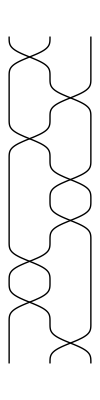
{{{8,17}},{8_17},{11-1/#1^3+4/#1^2-8/#1-8 #1+4 #1^2-#1^3&},{{}},{True},{True},{1},{-3+6 #1+12 #1^2-20 #1^3-24 #1^4+10 #1^5+16 #1^6+4 #1^7&},{KnotData[{8,17},BoundaryMeshRegion]},{7+1/#1^16-3/#1^12+5/#1^8-6/#1^4-6 #1^4+5 #1^8-3 #1^12+#1^16&},{-Graphics-},47,{0},{1},{{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&},{{Knot,{8,17}}},{9},{4},{{-5,-5}},{1},{False},{1}}
 |  |  |  |

```mathematica
Table[{KnotData[{8,17},w[[i]]]},{i,Length[w]}]
```

```mathematica
(*"AlexanderPolynomial"*)
```

```mathematica
11-1/#1^3+4/#1^2-8/#1-8 #1+4 #1^2-#1^3&/.#1->x
```

11-1/x^3+4/x^2-8/x-8 x+4 x^2-x^3&

```mathematica
ExpandAll[x^3*(11-1/x^3+4/x^2-8/x-8 x+4 x^2-x^3)]
```

-1+4 x-8 x^2+11 x^3-8 x^4+4 x^5-x^6

```mathematica
(*"BracketPolynomial"*)
```

```mathematica
7+1/#1^16-3/#1^12+5/#1^8-6/#1^4-6 #1^4+5 #1^8-3 #1^12+#1^16&/.#1->x
```

```mathematica
p[x_]=7+1/x^16-3/x^12+5/x^8-6/x^4-6 x^4+5 x^8-3 x^12+x^16
```

7+1/x^16-3/x^12+5/x^8-6/x^4-6 x^4+5 x^8-3 x^12+x^16

```mathematica
q[x_]=ExpandAll[x^16*p[x]]
```

1-3 x^4+5 x^8-6 x^12+7 x^16-6 x^20+5 x^24-3 x^28+x^32

```mathematica
f ={InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&;
```

```mathematica
g0=ParametricPlot3D[f[t],{t,0,2Pi}, Axes ->True,ViewPoint->Above]
```

```mathematica
ga=Graphics3D[{Orange, Specularity[White,70],KnotData[{8,17},"ImageData"]},Boxed-> False,ViewPoint-> {0,0.1,5}]
```

```mathematica
sp={Cos[t]*Sin[p],Sin[t]*Sin[p],Cos[p]}
```

{Cos[t] Sin[p],Sin[p] Sin[t],Cos[p]}

```mathematica
gb=ParametricPlot3D[sp,{t,-Pi,Pi},{p,0,Pi},ColorFunction->"Pastel",ImageSize->2000,PlotPoints->30,PlotStyle->Opacity[0.5],Mesh->False];
```

```mathematica
gout=Show[{ga,gb},PlotRange->All,Background->Black]
```

```mathematica
gout=Show[{g0,gb},PlotRange->All,Background->Black]
```